### Data

```mathematica
serum=0.01{1,2,3,4,5,6,7,8,9,10};
initial=0.01{2.3,14.6,23.9,35.4,45.8,54.9,64.8,74.6,83.3,91,98.3};
final[1]=0.01{{3.5,4.07,4.0,3.5,3.4,4.0,3.7,3.5,3.7,3.7},{6.5,9.1,12.4,12.1,14.8,15.3,15.8,17.4,19.8,22.1},{12.4,15.8,15.5,18.5,24.1,28.4,30.6,31.4,31.4,35.37},{20.0,23.3,28.0,31.8,28.47,36.3,42.1,41.4,41.7,40.6},{23.6,29.2,37.4,37.8,42.00,47.8,51.2,51.6,53.5,50.4},{37.2,33.1,49.9,45.0,55.2,53.8,57.3,61.5,61.8,57.6},{37.2,41.6,45.8,57.5,64.0,60.9,66.34,65.5,70.3,75.5},{51.0,53.9,63.6,70.2,74.01,71.1,74.2,73.4,78.6,79.5},{67.0,74.9,80.9,80.8,82.5,83.6,86.1,87.3,88.6,89.2},{77.4,82.4,87.5,91.3,92.4,92.4,93.9,96.2,95.4,94.1},{96.4,99.6,99.28,99.7,99.5,99.3,99.8,99.96,99.9,99.9}};
final[2]=0.01{{3.6,4.1,3.6,3.6,3.5,3.52,4.0,3.8,3.9,3.8},{7.0,9.6,11.7,12.3,16.2,15.3,17.1,17.3,19.9,22.5},{11.7,15.6,14.4,17.7,21.5,26.6,28.1,30.9,31.2,35.5},{18.5,23.12,26.2,28.5,31.6,35.6,42.8,38.6,38.6,43.9},{23.3,28.5,36.5,37.7,37.2,45.6,46.0,49.3,55.7,52.7},{29.2,34.6,45.6,45.9,47.6,54.2,60.6,62.6,64.7,60.8},{33.9,39.5,51.8,56.4,60.4,62.0,63.1,64.6,71.8,77.2},{49.8,57.5,60.4,70.4,71.0,73.0,71.91,77.0,78.7,78.3},{68.9,74.1,79.6,81.5,82.6,85.8,85.2,87.0,87.6,88.4},{78.4,82.2,88.7,91.4,92.7,93.5,93.4,95.0,95.9,95.8},{96.4,99.3,99.4,99.5,99.7,99.2,99.70,100.2,99.70,99.8}};
final[3]=0.01{{3.4,3.7,3.8,3.8,3.7,3.4,3.7,4.0,3.7,3.6},{6.2,9.7,11.9,12.9,15.92,16.0,16.4,17.6,19.6,22.4},{12.2,14.8,15.9,18.9,24.5,26.5,29.3,32.1,32.8,34.2},{20.2,26.9,26.87,31.1,31.1,36.0,42.6,40.2,42.1,44.0},{25.3,27.2,33.1,40.1,39.4,45.4,47.4,52.34,50.2,51.9},{36.3,34.0,49.9,43.5,48.8,51.7,54.7,58.1,58.6,64.6},{30.7,37.3,48.4,55.2,61.4,63.0,66.1,66.6,75.0,77.6},{50.92,57.3,59.1,70.5,74.3,72.6,74.5,75.2,75.4,80.5},{66.7,74.0,81.2,82.80,85.1,85.3,86.1,86.6,88.0,88.3},{78.6,83.7,88.9,90.9,91.1,93.4,94.9,95.5,95.6,95.9},{96.6,99.4,99.5,99.5,99.3,99.4,99.8,100.1,99.7,100.1}};final[4]=0.01{{3.8,3.8,3.7,4.0,3.5,3.4,3.8,3.4,3.5,3.4},{6.0,9.9,11.4,12.84,15.6,16.4,16.8,18.4,19.1,22.11},{12.1,15.9,15.14,17.9,24.7,27.7,28.8,33.3,33.4,36.81},{19.96,23.5,24.4,29.8,29.6,34.7,41.6,43.2,42.1,41.0},{24.1,24.7,33.0,39.4,41.7,47.2,52.84,48.2,50.3,53.3},{28.2,37.5,50.1,53.0,47.71,56.75,51.92,60.5,60.34,61.3},{30.6,35.9,50.9,52.6,61.4,63.9,66.0,70.6,72.2,78.0},{51.6,54.5,62.8,71.7,70.5,74.0,76.7,74.1,79.6,77.2},{66.5,74.1,81.6,83.2,83.1,86.0,86.33,87.5,89.3,87.5},{78.3,82.7,88.4,92.0,92.5,92.6,94.9,95.6,94.3,94.5},{96.6,99.7,99.1,99.5,99.1,99.6,99.69,99.7,99.6,99.6}};
```

### Plot Data

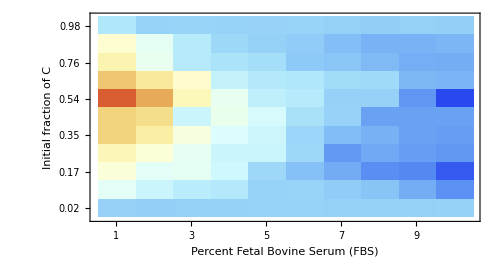

0.1175

```mathematica
e=1;
i=initial;
Ly=initial//Length;
Ls=10;
data=Table[
f=Median[{final[1],final[2],final[3],final[4]}];
(1-f⟦#,s⟧)-(1-i⟦#⟧)&/@Range[1,Ly,1]
,{s,1,10}
];
colors="LightTemperatureMap";
plotData=Table[data⟦i,11-j+1⟧,{j,1,11},{i,1,10}];
ArrayPlot[
plotData
,ColorFunction->colors
,AspectRatio->0.525
,Frame->True
,ImageSize->500
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}
,FrameTicks->{
{{#,ToString[Round[1-initial⟦#⟧,0.01]]}&/@Range[1,initial//Length,1],None}
,{#&/@Range[1,10,1],None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.005],Black]
,Axes->{True,False}
,FrameLabel->{"Initial fraction of C","Percent Fetal Bovine Serum (FBS)"}
]

extremity=Max[Max[data⟦All,3⟧],Abs[Min[data⟦All,3⟧]]]
scale={-extremity,extremity};
BarLegend[
{colors,scale}
(*,LegendLabel->"Critical number of compartments SubscriptBox[StyleBox[\"N\",FontSlant->\"Italic\"], \"crit\"]"*)
,LabelStyle->{FontSize->20,FontFamily->"Arial",Black}
,LegendLayout->"Row"
,LegendMarkerSize->300
]
```

### Data Fitting-Individual Replicates

```mathematica
Clear[data,nlm,e,i,Ly,Ls,y,t,y0,n,β,σ,α,κ,s]
α=.;
sol=ParametricNDSolve[
{
y'[t]==y[t](1-y[t])α((1+Exp[σ s])/(1+Exp[σ s-β(1/n+(n-1)/n y[t])])-(1+Exp[σ s])/(1+Exp[σ s-β(n-1)/n y[t]])-0.25),y[0]==y0
}
,y,{t,0,100},{y0,n,β,σ, s,α}
];

e=1;
i=initial;
Ly=initial//Length;
Ls=10;
data[e_]:=Flatten[
Table[
f=final[e];
{1-i⟦#⟧,serum⟦s⟧,(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
,{s,1,10}
]
,1];

fit[n_]:=Module[
{nlm},

nlm=NonlinearModelFit[data[#],y[x1,n,β,σ,x2,1.0][4]/.sol,{β,σ},{x1,x2}]&/@Range[1,4,1];
{nlm⟦#⟧["ParameterTableEntries"]⟦1,1⟧,nlm⟦#⟧["ParameterTableEntries"]⟦2,1⟧}&/@Range[1,4,1]
]
(*
{#,fit[#]}&/@Range[2,12,2]*)
```

```mathematica
{#,fit[#]}&/@Range[10,30,10]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{{10,{{3.10423,10.8507},{3.09265,10.901},{3.10794,10.7847},{3.10718,10.6541}}},{20,{{3.325,18.7324},{3.24735,19.0022},{3.29089,18.7671},{3.29957,18.5837}}},{30,{{3.41196,23.6794},{2.19846,2665.22},{3.24742,24.5431},{3.3287,23.8562}}}}

```mathematica
t={#,fit[#]}&/@Range[40,60,10]
Export[NotebookDirectory[]<>"nMed2.dat",t,"Data"]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

$Aborted

/Users/altrock/Dropbox/Projects_Dropbox/01_nonlinearPGG_2017/nonLinPGG_manuscript/Figures/F5/nMed2.dat

```mathematica
Export[NotebookDirectory[]<>"nMed.dat",{{10,{{3.10422101576861,-10.850785315318575},{3.093215193326062,-10.90004355056364},{3.107854536726392,-10.785510275239021},{3.107224119519835,-10.653306225726617}}},{20,{{3.324967224162417,-18.7328141576857},{3.2465154804808876,-19.004163746174864},{3.2908860988755455,-18.76708794162585},{3.29946068609572,-18.58400263914726}}},{30,{{3.413518409910899,-23.67068109867392},{2.1984586024680066,-3023.400171716267},{3.247416990587048,-24.543186219633963},{3.328704981091761,-23.85622705163837}}}},"Data"]
```

/Users/altrock/Dropbox/Projects_Dropbox/01_nonlinearPGG_2017/nonLinPGG_manuscript/Figures/F5/nMed.dat

#### Cleaning up

```mathematica
nβσ={{2,{{2.4624561237853486,9.007413617006167},{2.474142991624197,8.792565395476728},{2.4800627444792913,8.947953491727212},{2.5011614331300724,9.170711055414078}}},{4,{{2.8000510069719726,-0.16335958057132388},{2.7967426616188855,-0.2828878305168555},{2.806377692841307,-0.161097872296911},{2.8097953438274974,-0.01612351887105967}}},{6,{{2.937490576089887,-4.985775601613677},{2.9336584882488643,-5.063556032240257},{2.944279684848155,-4.950790128653232},{2.9451791863800865,-4.815735146846871}}},{8,{{3.031364915763749,-8.307543143646045},{3.0252599059080105,-8.363645417001154},{3.037685052480841,-8.252280032873015},{3.0372275055069857,-8.120518789496467}}},{10,{{3.10422101576861,-10.850785315318575},{3.093215193326062,-10.90004355056364},{3.107854536726392,-10.785510275239021},{3.107224119519835,-10.653306225726617}}},{12,{{3.163681604664562,-12.916784651047191},{3.145121560700123,-12.973133804521748},{3.163400839332592,-12.849698284280063},{3.162386313285028,-12.715769074034906}}}};

nβσM={{10,{{3.10422101576861,-10.850785315318575},{3.093215193326062,-10.90004355056364},{3.107854536726392,-10.785510275239021},{3.107224119519835,-10.653306225726617}}},{20,{{3.324967224162417,-18.7328141576857},{3.2465154804808876,-19.004163746174864},{3.2908860988755455,-18.76708794162585},{3.29946068609572,-18.58400263914726}}},{30,{{3.413518409910899,-23.67068109867392},{2.1984586024680066,-3023.400171716267},{3.247416990587048,-24.543186219633963},{3.328704981091761,-23.85622705163837}}}};
```

{{2,2.4771},{4,2.80321},{6,2.94089},{8,3.0343},{10,3.10572},{12,3.16289}}

{{2,-8.97768},{4,0.162229},{6,4.96828},{8,8.27991},{10,10.8181},{12,12.8832}}

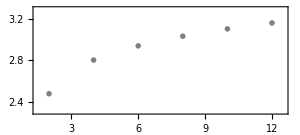

{{2,2.4771},{4,2.80321},{6,2.94089},{8,3.0343},{10,3.10572},{12,3.16289}}

{{2,-8.97768},{4,0.162229},{6,4.96828},{8,8.27991},{10,10.8181},{12,12.8832}}

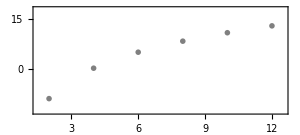

```mathematica
nβ={nβσ⟦#,1⟧,Median[Table[nβσ⟦#,2,l,1⟧,{l,1,4}]]}&/@Range[1,nβσ//Length,1]
nσ={nβσ⟦#,1⟧,Median[Table[-nβσ⟦#,2,l,2⟧,{l,1,4}]]}&/@Range[1,nβσ//Length,1]
marker=Graphics[{Gray,Disk[]}];
ListPlot[
nβ
,PlotMarkers->{marker,0.11}
,Frame->True
,PlotRange->{{1.5,12.5},{2.3,3.3}}
,ImageSize->300
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.45
,FrameLabel->{{None,None},{"Neighborhood size n","MLE of β"(*"n=8, σ=β/2"*)}}
,Axes->{True,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
(*,PlotLegends->{Placed[{"n=15","n=25"},{0.8,0.75}]}*)
]
nβ={nβσ⟦#,1⟧,Median[Table[nβσ⟦#,2,l,1⟧,{l,1,4}]]}&/@Range[1,nβσ//Length,1]
nσ={nβσ⟦#,1⟧,Median[Table[-nβσ⟦#,2,l,2⟧,{l,1,4}]]}&/@Range[1,nβσ//Length,1]

ListPlot[
nσ
,PlotMarkers->{marker,0.11}
,Frame->True
,PlotRange->{{1.5,12.5},{-13,18}}
,ImageSize->300
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.45
,FrameLabel->{{None,None},{"Neighborhood size n","MLE of σ(%serum)"(*"n=8, σ=β/2"*)}}
,Axes->{False,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
(*,PlotLegends->{Placed[{"n=15","n=25"},{0.8,0.75}]}*)
]
```

### Data Fitting-All data

#### Discrete Time, 2D model fit

```mathematica
y[Δt_,y0_,n_,σ_,β_,κ_,α_]:=y0+Δt(y0(1-y0)α((1+Exp[σ])/(1+Exp[σ-β(1/n+(n-1)/n y0)])-(1+Exp[σ])/(1+Exp[σ-β(n-1)/n y0])-κ))
g[n_,σ_,β_,init_]:=y[4.,init,n,σ,β,0.1,1.0]
e=1;
i=initial;
Ly=initial//Length;
Ls=10;
data=Flatten[
Table[
f=final[e];
{1-i⟦#⟧,serum⟦s⟧,(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
,{e,1,4}
,{s,1,10}
]
,2];
data//Dimensions

nlm=NonlinearModelFit[data,g[n,y σ,β,x],{β,σ,n},{x ,y}];

nlm["ParameterTable"]
```

{440,3}

| Estimate | Standard Error | t-Statistic | P-Value
β | 2.1754 | 0.114564 | 18.9885 | 4.59241×10^-59
σ | -27.105 | 0.673654 | -40.2358 | 4.85719×10^-149
n | 1.75499 | 0.0490686 | 35.766 | 6.86847×10^-132

#### ParametricODE, 2D model fit

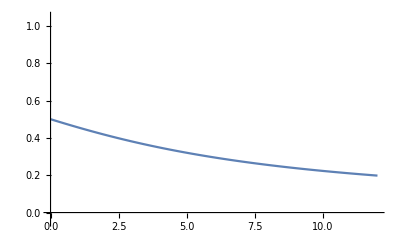

```mathematica
Clear[y,t,y0,n,β,σ,α,κ,s]
α=.;
sol=ParametricNDSolve[
{
y'[t]==y[t](1-y[t])α((1+Exp[-σ s])/(1+Exp[-σ s-β(1/n+(n-1)/n y[t])])-(1+Exp[-σ s])/(1+Exp[-σ s-β(n-1)/n y[t]])-0.25),y[0]==y0
}
,y,{t,0,100},{y0,n,β,σ, s,α}
];

Plot[
Evaluate[y[0.5,10,5.,2.,0.01,1][t]/.sol],{t,0,12}
,PlotRange->{All,{-0.05,1.05}}
]
```

```mathematica
e=1;
i=initial;
Ly=initial//Length;
Ls=10;
data=Flatten[
Table[
f=final[e];
{1-i⟦#⟧,serum⟦s⟧,(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
,{e,1,4}
,{s,1,10}
]
,2];
data//Dimensions

fit[n_]:=Module[
{nlm},

nlm=NonlinearModelFit[data,y[x1,n,β,σ,x2,1.0][4]/.sol,{β,σ},{x1,x2}];

{nlm["ParameterTable"],nlm["BIC"]}
]

(*Table[{n,fit[n]⟦2⟧},{n,2,20,2}]*)
fit[2]
fit[6]
```

{440,3}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{ | Estimate | Standard Error | t-Statistic | P-Value
β | 2.47981 | 0.0917111 | 27.0394 | 2.01056×10^-95
σ | 8.97966 | 0.284242 | 31.5916 | 5.29427×10^-115,-1430.49}

{ | Estimate | Standard Error | t-Statistic | P-Value
β | 2.94018 | 0.239597 | 12.2713 | 5.87033×10^-30
σ | -4.9542 | 0.689843 | -7.18165 | 2.97746×10^-12,-629.435}

#### Parameter Testing

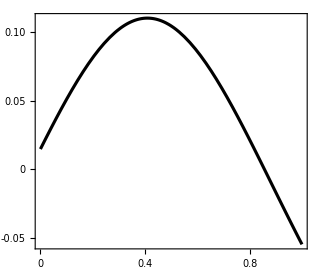

```mathematica
rC[y_,β_,σ_,n_]:=γ If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (1+y(n-1))/n-σ)])]-κ;
rD[y_,β_,σ_,n_]:=γ If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (y(n-1))/n-σ)])];
γ=1.;
κ=0.25;
s=0.12;
Plot[
{
rC[y,3.1,10.8 s,10]-rD[y,3.1,10.8s,10]
},{y,0,1}
,PlotStyle->{{Thickness[0.007],Black},{Thickness[0.007],Red,Dashed}}
,Frame->True
,PlotRange->All
,ImageSize->320
,LabelStyle->{FontSize->16,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.85
(*,FrameLabel->{{"r_C-r_D",None},{"Frequency of C",None(*"n=8, σ=β/2"*)}}*)
,Axes->{True,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
(*,PlotLegends->{Placed[{"n=15","n=25"},{0.8,0.75}]}*)
]
```

#### ParametricODE, 2D model fit, σ fixed

```mathematica
Clear[y,t,y0,n,β,σ,α,κ,s]

sol=ParametricNDSolve[
{
y'[t]==y[t](1-y[t])1.0((1+Exp[-σ s])/(1+Exp[-σ s-β(1/n+(n-1)/n y[t])])-(1+Exp[-σ s])/(1+Exp[-σ s-β(n-1)/n y[t]])-0.25),y[0]==y0
}
,y,{t,0,100},{y0,n,β,σ, s}
];
e=1;
i=initial;
Ly=initial//Length;
Ls=10;
data=Flatten[
Table[
f=final[e];
{1-i⟦#⟧,serum⟦s⟧,(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
,{e,1,4}
,{s,1,10}
]
,2];
data//Dimensions


nlm=NonlinearModelFit[data,y[x1,n,β,1,x2][4]/.sol,{β,n},{x1,x2}];

{nlm["ParameterTable"],nlm["BIC"]}
```

{440,3}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{ | Estimate | Standard Error | t-Statistic | P-Value
β | 1.63112 | 0.186252 | 8.75762 | 4.38639×10^-17
n | 2.26438 | 0.181484 | 12.477 | 8.7991×10^-31,-998.584}

```mathematica
(*Table[{n,fit[n]⟦2⟧},{n,2,20,2}]*)
fit[2]
```

{440,3}

{ | Estimate | Standard Error | t-Statistic | P-Value
β | 2.47981 | 0.0917111 | 27.0394 | 2.01055×10^-95
σ | 8.97966 | 0.284242 | 31.5916 | 5.2943×10^-115,-1430.49}

```mathematica
fit[6]
fit[10]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
β | 2.94018 | 0.239597 | 12.2713 | 5.87033×10^-30
σ | -4.9542 | 0.689843 | -7.18165 | 2.97746×10^-12,-629.435}

#### Does α matter?

```mathematica
κ=0.25;
rC[y_,β_,σ_,n_,α_]:=α If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (1+y(n-1))/n-σ)])]-α κ;
rD[y_,β_,σ_,n_,α_]:=α If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (y(n-1))/n-σ)])];
Manipulate[
Plot[
{
rC[y,β,σ s,n,α],rD[y,β,-σ s,n,α]
},{y,0,1}
,PlotStyle->{{Thickness[0.007],Black},{Thickness[0.007],Red,Dashed}}
,Frame->True
,PlotRange->All
,ImageSize->320
,LabelStyle->{FontSize->16,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.85
(*,FrameLabel->{{"r_C-r_D",None},{"Frequency of C",None(*"n=8, σ=β/2"*)}}*)
,Axes->{True,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
(*,PlotLegends->{Placed[{"n=15","n=25"},{0.8,0.75}]}*)
]
,{n,2,6,2}
,{β,2,3,0.1}
,{σ,-9,5,1}
,{s,0.01,0.2,0.02}
,{{α,1},0,2,0.01}
]
```

### Fixed n (large)

```mathematica
Clear[data,nlm,e,i,Ly,Ls,y,t,y0,n,β,σ,α,κ,s]
α=.;
sol=ParametricNDSolve[
{
y'[t]==y[t](1-y[t])α((1+Exp[-σ s])/(1+Exp[-σ s-β(1/n+(n-1)/n y[t])])-(1+Exp[-σ s])/(1+Exp[-σ s-β(n-1)/n y[t]])-0.25),y[0]==y0
}
,y,{t,0,100},{y0,n,β,σ, s,α}
];

e=1;
i=initial;
Ly=initial//Length;
Ls=10;
data[e_]:=Flatten[
Table[
f=final[e];
{1-i⟦#⟧,serum⟦s⟧,(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
,{s,1,10}
]
,1];

fit[n_]:=Module[
{nlm},

nlm=NonlinearModelFit[data[#],y[x1,n,β,σ,x2,1.0][4]/.sol,{β,σ},{x1,x2}]&/@Range[1,4,1];
{nlm⟦#⟧["ParameterTableEntries"]⟦1,1⟧,nlm⟦#⟧["ParameterTableEntries"]⟦2,1⟧}&/@Range[1,4,1]
]

nLarge={#,fit[#]}&/@Range[10,100,10]

Export[NotebookDirectory[]<>"nLarge.dat",nLarge,"Data"]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

### Data fit variable n, κ fixed

#### fit

```mathematica
(*Clear[data,fit,nlm,y,t,y0,n,β,σ,α,κ,s]*)
Clear[β,σ,κ,n,y0,s];
serum=0.01{1,2,3,4,5,6,7,8,9,10};
initial=0.01{2.3,14.6,23.9,35.4,45.8,54.9,64.8,74.6,83.3,91,98.3};
final[1]=0.01{{3.5,4.07,4.0,3.5,3.4,4.0,3.7,3.5,3.7,3.7},{6.5,9.1,12.4,12.1,14.8,15.3,15.8,17.4,19.8,22.1},{12.4,15.8,15.5,18.5,24.1,28.4,30.6,31.4,31.4,35.37},{20.0,23.3,28.0,31.8,28.47,36.3,42.1,41.4,41.7,40.6},{23.6,29.2,37.4,37.8,42.00,47.8,51.2,51.6,53.5,50.4},{37.2,33.1,49.9,45.0,55.2,53.8,57.3,61.5,61.8,57.6},{37.2,41.6,45.8,57.5,64.0,60.9,66.34,65.5,70.3,75.5},{51.0,53.9,63.6,70.2,74.01,71.1,74.2,73.4,78.6,79.5},{67.0,74.9,80.9,80.8,82.5,83.6,86.1,87.3,88.6,89.2},{77.4,82.4,87.5,91.3,92.4,92.4,93.9,96.2,95.4,94.1},{96.4,99.6,99.28,99.7,99.5,99.3,99.8,99.96,99.9,99.9}};
final[2]=0.01{{3.6,4.1,3.6,3.6,3.5,3.52,4.0,3.8,3.9,3.8},{7.0,9.6,11.7,12.3,16.2,15.3,17.1,17.3,19.9,22.5},{11.7,15.6,14.4,17.7,21.5,26.6,28.1,30.9,31.2,35.5},{18.5,23.12,26.2,28.5,31.6,35.6,42.8,38.6,38.6,43.9},{23.3,28.5,36.5,37.7,37.2,45.6,46.0,49.3,55.7,52.7},{29.2,34.6,45.6,45.9,47.6,54.2,60.6,62.6,64.7,60.8},{33.9,39.5,51.8,56.4,60.4,62.0,63.1,64.6,71.8,77.2},{49.8,57.5,60.4,70.4,71.0,73.0,71.91,77.0,78.7,78.3},{68.9,74.1,79.6,81.5,82.6,85.8,85.2,87.0,87.6,88.4},{78.4,82.2,88.7,91.4,92.7,93.5,93.4,95.0,95.9,95.8},{96.4,99.3,99.4,99.5,99.7,99.2,99.70,100.2,99.70,99.8}};
final[3]=0.01{{3.4,3.7,3.8,3.8,3.7,3.4,3.7,4.0,3.7,3.6},{6.2,9.7,11.9,12.9,15.92,16.0,16.4,17.6,19.6,22.4},{12.2,14.8,15.9,18.9,24.5,26.5,29.3,32.1,32.8,34.2},{20.2,26.9,26.87,31.1,31.1,36.0,42.6,40.2,42.1,44.0},{25.3,27.2,33.1,40.1,39.4,45.4,47.4,52.34,50.2,51.9},{36.3,34.0,49.9,43.5,48.8,51.7,54.7,58.1,58.6,64.6},{30.7,37.3,48.4,55.2,61.4,63.0,66.1,66.6,75.0,77.6},{50.92,57.3,59.1,70.5,74.3,72.6,74.5,75.2,75.4,80.5},{66.7,74.0,81.2,82.80,85.1,85.3,86.1,86.6,88.0,88.3},{78.6,83.7,88.9,90.9,91.1,93.4,94.9,95.5,95.6,95.9},{96.6,99.4,99.5,99.5,99.3,99.4,99.8,100.1,99.7,100.1}};final[4]=0.01{{3.8,3.8,3.7,4.0,3.5,3.4,3.8,3.4,3.5,3.4},{6.0,9.9,11.4,12.84,15.6,16.4,16.8,18.4,19.1,22.11},{12.1,15.9,15.14,17.9,24.7,27.7,28.8,33.3,33.4,36.81},{19.96,23.5,24.4,29.8,29.6,34.7,41.6,43.2,42.1,41.0},{24.1,24.7,33.0,39.4,41.7,47.2,52.84,48.2,50.3,53.3},{28.2,37.5,50.1,53.0,47.71,56.75,51.92,60.5,60.34,61.3},{30.6,35.9,50.9,52.6,61.4,63.9,66.0,70.6,72.2,78.0},{51.6,54.5,62.8,71.7,70.5,74.0,76.7,74.1,79.6,77.2},{66.5,74.1,81.6,83.2,83.1,86.0,86.33,87.5,89.3,87.5},{78.3,82.7,88.4,92.0,92.5,92.6,94.9,95.6,94.3,94.5},{96.6,99.7,99.1,99.5,99.1,99.6,99.69,99.7,99.6,99.6}};
e=1;
i=initial;
Ly=initial//Length;
Ls=10;
fitData[e_,s_]:=Module[{f},
f=final[e];
{serum⟦s⟧,
{1-i⟦#⟧,(1-f⟦#,s⟧)}&/@Range[1,Ly,1]
}
]
Clear[fd,β,σ,n,κ,d,t]
fd[ser_]:=Flatten[fitData[#,ser]⟦2⟧&/@Range[1,4,1],1]
fitting[nn_,ser_]:=Module[
{sol,d,L,cost,nlm,βfitted,σfitted},
Clear[β,σ,κ,n,y0];
sol=ParametricNDSolve[
{
y'[t]==y[t](1-y[t])α((1+Exp[σ])/(1+Exp[σ-β(1/n+(n-1)/n y[t])])-(1+Exp[σ])/(1+Exp[σ-β(n-1)/n y[t]])-κ),y[0]==y0
}
,y,{t,0,100},{y0,n,β,σ,α,κ}
];

d=fd[ser];
L=Length[d];
cost=0.25;
nlm=NonlinearModelFit[d,y[x1,nn,β,σ,1.0,cost][4]/.sol,{β,σ},{x1}];
(* nlm["ParameterTable"] *)
βfitted=nlm["ParameterTableEntries"]⟦1,1⟧;
σfitted=nlm["ParameterTableEntries"]⟦2,1⟧;

(*ListPlot[
{
{d⟦#,1⟧,(y[d⟦#,1⟧,n,βfitted,σfitted,1.0,cost][4]/.sol)}&/@Range[1,L,1]
,
{d⟦#,1⟧,d⟦#,2⟧}&/@Range[1,L,1]
}
,Frame->True
,PlotRange->{{-0.05,1.05},Automatic}
,PlotStyle->{Red,Black}
]*)

{βfitted,σfitted}
]
fitting[#,2]&/@Range[4,40,4]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{{2.12282,0.906095},{3.04028,1.39502},{3.6383,1.70771},{4.08351,1.93859},{4.43873,2.122},{4.73425,2.27441},{4.98664,2.40504},{5.20693,2.51947},{5.40252,2.62142},{5.57906,2.71341}}

```mathematica
T=Table[
fitting[#,s]&/@Range[4,40,1]
,{s,1,10,1}
]

Export[NotebookDirectory[]<>"XserumFitLong.dat",T]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{{{2.26301,0.988746},{2.54755,1.14313},{2.79293,1.27401},{3.00827,1.38791},{3.19993,1.48888},{3.37256,1.57961},{3.52962,1.66201},{3.67375,1.7375},{3.807,1.80716},{3.93097,1.87183},{4.04692,1.93218},{4.1559,1.98876},{4.25872,2.04203},{4.35605,2.09235},{4.44839,2.14004},{4.5362,2.18539},{4.61999,2.22859},{4.69992,2.26986},{4.77637,2.30937},{4.8496,2.34727},{4.91958,2.3837},{4.98667,2.41876},{5.05102,2.45256},{5.11247,2.48522},{5.17186,2.51676},{5.2287,2.5473},{5.28332,2.57689},{5.33561,2.60562},{5.38596,2.6335},{5.43433,2.66061},{5.4809,2.68699},{5.5257,2.71268},{5.56865,2.73773},{5.6104,2.76215},{5.65105,2.78595},{5.69019,2.80922},{5.72829,2.83195}},{{2.12282,0.906095},{2.40066,1.05641},{2.64091,1.18431},{2.85194,1.29597},{3.04028,1.39502},{3.21006,1.48413},{3.36479,1.56507},{3.50689,1.63925},{3.6383,1.70771},{3.76059,1.77127},{3.87491,1.8306},{3.98228,1.88622},{4.08351,1.93859},{4.17925,1.98806},{4.27007,2.03495},{4.35646,2.07952},{4.43873,2.122},{4.51745,2.16256},{4.59273,2.20139},{4.66492,2.23863},{4.73425,2.27441},{4.80086,2.30885},{4.86503,2.34204},{4.92692,2.37407},{4.98664,2.40504},{5.04448,2.43498},{5.10028,2.46401},{5.1545,2.49215},{5.20693,2.51947},{5.25791,2.54601},{5.30725,2.57184},{5.35562,2.59695},{5.40252,2.62142},{5.44854,2.64524},{5.49295,2.66852},{5.53653,2.69123},{5.57906,2.71341}},{{1.77464,0.836278},{2.04088,0.964288},{2.27239,1.07666},{2.47712,1.17656},{2.66059,1.26637},{2.82682,1.34787},{2.97879,1.42243},{3.11879,1.49111},{3.24857,1.55476},{3.36955,1.61406},{3.48284,1.66956},{3.58956,1.72169},{3.6901,1.7709},{3.78556,1.81741},{3.8762,1.86156},{3.9625,1.90357},{4.04498,1.94362},{4.12393,1.9819},{4.19956,2.01857},{4.2724,2.05372},{4.34229,2.08753},{4.40999,2.12003},{4.47492,2.15141},{4.53808,2.18164},{4.59905,2.21088},{4.65795,2.23918},{4.71548,2.26656},{4.77118,2.29312},{4.82494,2.31893},{4.87794,2.34393},{4.92928,2.36826},{4.97929,2.39193},{5.02756,2.41503},{5.07564,2.43745},{5.12215,2.45934},{5.16751,2.48071},{5.21205,2.50157}},{{1.4792,0.924463},{1.74357,1.00914},{1.97071,1.09653},{2.17012,1.1802},{2.34786,1.25864},{2.50817,1.33174},{2.65413,1.39985},{2.78808,1.46341},{2.91182,1.5229},{3.0268,1.57875},{3.13416,1.63133},{3.23483,1.68097},{3.32961,1.72797},{3.41914,1.77259},{3.50398,1.81504},{3.58457,1.85551},{3.66141,1.89417},{3.73464,1.93121},{3.80477,1.9667},{3.87197,2.0008},{3.93652,2.0336},{3.99858,2.0652},{4.05836,2.09567},{4.11599,2.12511},{4.17154,2.15359},{4.22548,2.18111},{4.27751,2.20782},{4.32805,2.23369},{4.37701,2.25882},{4.42451,2.28324},{4.47061,2.307},{4.51559,2.33009},{4.55928,2.35259},{4.60181,2.37451},{4.64329,2.39589},{4.68334,2.41681},{4.72316,2.43712}},{{1.46236,0.773202},{1.70923,0.877951},{1.92336,0.976095},{2.11241,1.06638},{2.28152,1.14927},{2.4344,1.22555},{2.57381,1.29603},{2.70187,1.36144},{2.82021,1.42241},{2.93022,1.47946},{3.03293,1.53304},{3.12923,1.58352},{3.21986,1.63124},{3.30543,1.67648},{3.38647,1.71947},{3.46342,1.76042},{3.53666,1.79951},{3.60654,1.8369},{3.67336,1.87273},{3.73733,1.90713},{3.79871,1.9402},{3.85769,1.97204},{3.91446,2.00274},{3.96915,2.03238},{4.02195,2.06102},{4.07294,2.08873},{4.12225,2.11558},{4.17,2.1416},{4.21627,2.16686},{4.26115,2.19139},{4.30473,2.21524},{4.34709,2.23844},{4.38826,2.26103},{4.42836,2.28303},{4.46737,2.30449},{4.50541,2.32542},{4.5425,2.34585}},{{1.65271,0.422092},{1.86442,0.58054},{2.05643,0.709819},{2.23068,0.820063},{2.38946,0.916685},{2.53506,1.00289},{2.66927,1.08084},{2.79365,1.15202},{2.90946,1.21757},{3.01772,1.27834},{3.11941,1.33496},{3.21517,1.38798},{3.30565,1.43785},{3.39141,1.48491},{3.47289,1.52946},{3.55048,1.57177},{3.62452,1.61205},{3.69535,1.65048},{3.76322,1.68722},{3.82834,1.72243},{3.89102,1.7562},{3.951,1.78871},{4.00924,1.81996},{4.06529,1.85011},{4.11945,1.87921},{4.17182,1.90733},{4.22256,1.93455},{4.27172,1.96091},{4.31942,1.98646},{4.36573,2.01127},{4.41074,2.03536},{4.45451,2.05878},{4.49716,2.08156},{4.5386,2.10375},{4.57903,2.12537},{4.61845,2.14644},{4.65693,2.167}},{{1.72032,0.209585},{1.90619,0.386307},{2.08102,0.527083},{2.243,0.645103},{2.39277,0.747218},{2.5315,0.83749},{2.66044,0.918535},{2.7807,0.992157},{2.89327,1.05965},{2.99898,1.122},{3.0986,1.17995},{3.19274,1.23409},{3.28195,1.2849},{3.36669,1.33278},{3.44738,1.37804},{3.52437,1.42097},{3.59798,1.46179},{3.66848,1.5007},{3.73612,1.53788},{3.80112,1.57347},{3.86367,1.6076},{3.92394,1.64039},{3.98209,1.67194},{4.03828,1.70234},{4.0926,1.73167},{4.14519,1.76001},{4.19615,1.78741},{4.24558,1.81395},{4.29357,1.83967},{4.34017,1.86462},{4.38552,1.88885},{4.42964,1.91239},{4.47259,1.93529},{4.51445,1.95758},{4.55522,1.9793},{4.59508,2.00046},{4.63395,2.0211}},{{1.59553,0.171764},{1.77582,0.344805},{1.94533,0.482627},{2.10251,0.598241},{2.24796,0.698395},{2.38278,0.787045},{2.50816,0.866725},{2.62513,0.939191},{2.73466,1.0057},{2.83751,1.06719},{2.93442,1.12439},{3.02598,1.17788},{3.11272,1.22811},{3.19511,1.27547},{3.27352,1.32027},{3.3483,1.36277},{3.41976,1.40322},{3.48818,1.44178},{3.55377,1.47864},{3.61678,1.51393},{3.67736,1.5478},{3.73569,1.58034},{3.79197,1.61165},{3.84629,1.64184},{3.89878,1.67097},{3.94956,1.69911},{3.99873,1.72634},{4.0465,1.7527},{4.09264,1.77827},{4.13754,1.80307},{4.18117,1.82716},{4.2236,1.85057},{4.26529,1.87332},{4.3051,1.89551},{4.34426,1.9171},{4.38227,1.93818},{4.41964,1.9587}},{{1.18635,0.341004},{1.37247,0.469618},{1.54177,0.577534},{1.69634,0.671637},{1.8381,0.755622},{1.96882,0.83167},{2.08974,0.901382},{2.20231,0.965694},{2.30745,1.02545},{2.40599,1.08128},{2.49877,1.13363},{2.58632,1.18295},{2.66909,1.2296},{2.74766,1.27381},{2.82237,1.31585},{2.89358,1.3559},{2.96159,1.39415},{3.02659,1.43077},{3.08899,1.46585},{3.14884,1.49956},{3.20636,1.53198},{3.26178,1.5632},{3.31517,1.59332},{3.3667,1.62241},{3.41649,1.65053},{3.46466,1.67775},{3.51129,1.70412},{3.55648,1.7297},{3.60032,1.75452},{3.64288,1.77865},{3.68437,1.80207},{3.72452,1.8249},{3.7636,1.84714},{3.80171,1.86879},{3.83885,1.88991},{3.87504,1.91049},{3.91039,1.93062}},{{1.34737,0.053649},{1.50939,0.221374},{1.66182,0.355142},{1.80413,0.467275},{1.93647,0.564553},{2.05958,0.650857},{2.17443,0.728611},{2.28187,0.799495},{2.38325,0.864495},{2.47759,0.925102},{2.56716,0.981404},{2.65187,1.03416},{2.73235,1.08376},{2.80876,1.13062},{2.88161,1.175},{2.95119,1.21716},{3.01776,1.25731},{3.08151,1.29566},{3.14302,1.33226},{3.20151,1.36751},{3.25815,1.40126},{3.31271,1.43374},{3.36538,1.46501},{3.41624,1.49518},{3.46546,1.52431},{3.51305,1.55249},{3.55923,1.57975},{3.60399,1.60617},{3.6475,1.63179},{3.68973,1.65666},{3.73076,1.68084},{3.77072,1.70434},{3.80972,1.7272},{3.84764,1.74947},{3.8846,1.77118},{3.92071,1.79234},{3.95595,1.81299}}}

/Users/altrock/Dropbox/Projects_Dropbox/01_nonlinearPGG_2017/nonLinPGG_manuscript/Figures/F5/serumFitLong.dat

```mathematica
T
```

{{{2.26301,0.988746},{2.54755,1.14313},{2.79293,1.27401},{3.00827,1.38791},{3.19993,1.48888},{3.37256,1.57961},{3.52962,1.66201},{3.67375,1.7375},{3.807,1.80716},{3.93097,1.87183},{4.04692,1.93218},{4.1559,1.98876},{4.25872,2.04203},{4.35605,2.09235},{4.44839,2.14004},{4.5362,2.18539},{4.61999,2.22859},{4.69992,2.26986},{4.77637,2.30937},{4.8496,2.34727},{4.91958,2.3837},{4.98667,2.41876},{5.05102,2.45256},{5.11247,2.48522},{5.17186,2.51676},{5.2287,2.5473},{5.28332,2.57689},{5.33561,2.60562},{5.38596,2.6335},{5.43433,2.66061},{5.4809,2.68699},{5.5257,2.71268},{5.56865,2.73773},{5.6104,2.76215},{5.65105,2.78595},{5.69019,2.80922},{5.72829,2.83195}},{{2.12282,0.906095},{2.40066,1.05641},{2.64091,1.18431},{2.85194,1.29597},{3.04028,1.39502},{3.21006,1.48413},{3.36479,1.56507},{3.50689,1.63925},{3.6383,1.70771},{3.76059,1.77127},{3.87491,1.8306},{3.98228,1.88622},{4.08351,1.93859},{4.17925,1.98806},{4.27007,2.03495},{4.35646,2.07952},{4.43873,2.122},{4.51745,2.16256},{4.59273,2.20139},{4.66492,2.23863},{4.73425,2.27441},{4.80086,2.30885},{4.86503,2.34204},{4.92692,2.37407},{4.98664,2.40504},{5.04448,2.43498},{5.10028,2.46401},{5.1545,2.49215},{5.20693,2.51947},{5.25791,2.54601},{5.30725,2.57184},{5.35562,2.59695},{5.40252,2.62142},{5.44854,2.64524},{5.49295,2.66852},{5.53653,2.69123},{5.57906,2.71341}},{{1.77464,0.836278},{2.04088,0.964288},{2.27239,1.07666},{2.47712,1.17656},{2.66059,1.26637},{2.82682,1.34787},{2.97879,1.42243},{3.11879,1.49111},{3.24857,1.55476},{3.36955,1.61406},{3.48284,1.66956},{3.58956,1.72169},{3.6901,1.7709},{3.78556,1.81741},{3.8762,1.86156},{3.9625,1.90357},{4.04498,1.94362},{4.12393,1.9819},{4.19956,2.01857},{4.2724,2.05372},{4.34229,2.08753},{4.40999,2.12003},{4.47492,2.15141},{4.53808,2.18164},{4.59905,2.21088},{4.65795,2.23918},{4.71548,2.26656},{4.77118,2.29312},{4.82494,2.31893},{4.87794,2.34393},{4.92928,2.36826},{4.97929,2.39193},{5.02756,2.41503},{5.07564,2.43745},{5.12215,2.45934},{5.16751,2.48071},{5.21205,2.50157}},{{1.4792,0.924463},{1.74357,1.00914},{1.97071,1.09653},{2.17012,1.1802},{2.34786,1.25864},{2.50817,1.33174},{2.65413,1.39985},{2.78808,1.46341},{2.91182,1.5229},{3.0268,1.57875},{3.13416,1.63133},{3.23483,1.68097},{3.32961,1.72797},{3.41914,1.77259},{3.50398,1.81504},{3.58457,1.85551},{3.66141,1.89417},{3.73464,1.93121},{3.80477,1.9667},{3.87197,2.0008},{3.93652,2.0336},{3.99858,2.0652},{4.05836,2.09567},{4.11599,2.12511},{4.17154,2.15359},{4.22548,2.18111},{4.27751,2.20782},{4.32805,2.23369},{4.37701,2.25882},{4.42451,2.28324},{4.47061,2.307},{4.51559,2.33009},{4.55928,2.35259},{4.60181,2.37451},{4.64329,2.39589},{4.68334,2.41681},{4.72316,2.43712}},{{1.46236,0.773202},{1.70923,0.877951},{1.92336,0.976095},{2.11241,1.06638},{2.28152,1.14927},{2.4344,1.22555},{2.57381,1.29603},{2.70187,1.36144},{2.82021,1.42241},{2.93022,1.47946},{3.03293,1.53304},{3.12923,1.58352},{3.21986,1.63124},{3.30543,1.67648},{3.38647,1.71947},{3.46342,1.76042},{3.53666,1.79951},{3.60654,1.8369},{3.67336,1.87273},{3.73733,1.90713},{3.79871,1.9402},{3.85769,1.97204},{3.91446,2.00274},{3.96915,2.03238},{4.02195,2.06102},{4.07294,2.08873},{4.12225,2.11558},{4.17,2.1416},{4.21627,2.16686},{4.26115,2.19139},{4.30473,2.21524},{4.34709,2.23844},{4.38826,2.26103},{4.42836,2.28303},{4.46737,2.30449},{4.50541,2.32542},{4.5425,2.34585}},{{1.65271,0.422092},{1.86442,0.58054},{2.05643,0.709819},{2.23068,0.820063},{2.38946,0.916685},{2.53506,1.00289},{2.66927,1.08084},{2.79365,1.15202},{2.90946,1.21757},{3.01772,1.27834},{3.11941,1.33496},{3.21517,1.38798},{3.30565,1.43785},{3.39141,1.48491},{3.47289,1.52946},{3.55048,1.57177},{3.62452,1.61205},{3.69535,1.65048},{3.76322,1.68722},{3.82834,1.72243},{3.89102,1.7562},{3.951,1.78871},{4.00924,1.81996},{4.06529,1.85011},{4.11945,1.87921},{4.17182,1.90733},{4.22256,1.93455},{4.27172,1.96091},{4.31942,1.98646},{4.36573,2.01127},{4.41074,2.03536},{4.45451,2.05878},{4.49716,2.08156},{4.5386,2.10375},{4.57903,2.12537},{4.61845,2.14644},{4.65693,2.167}},{{1.72032,0.209585},{1.90619,0.386307},{2.08102,0.527083},{2.243,0.645103},{2.39277,0.747218},{2.5315,0.83749},{2.66044,0.918535},{2.7807,0.992157},{2.89327,1.05965},{2.99898,1.122},{3.0986,1.17995},{3.19274,1.23409},{3.28195,1.2849},{3.36669,1.33278},{3.44738,1.37804},{3.52437,1.42097},{3.59798,1.46179},{3.66848,1.5007},{3.73612,1.53788},{3.80112,1.57347},{3.86367,1.6076},{3.92394,1.64039},{3.98209,1.67194},{4.03828,1.70234},{4.0926,1.73167},{4.14519,1.76001},{4.19615,1.78741},{4.24558,1.81395},{4.29357,1.83967},{4.34017,1.86462},{4.38552,1.88885},{4.42964,1.91239},{4.47259,1.93529},{4.51445,1.95758},{4.55522,1.9793},{4.59508,2.00046},{4.63395,2.0211}},{{1.59553,0.171764},{1.77582,0.344805},{1.94533,0.482627},{2.10251,0.598241},{2.24796,0.698395},{2.38278,0.787045},{2.50816,0.866725},{2.62513,0.939191},{2.73466,1.0057},{2.83751,1.06719},{2.93442,1.12439},{3.02598,1.17788},{3.11272,1.22811},{3.19511,1.27547},{3.27352,1.32027},{3.3483,1.36277},{3.41976,1.40322},{3.48818,1.44178},{3.55377,1.47864},{3.61678,1.51393},{3.67736,1.5478},{3.73569,1.58034},{3.79197,1.61165},{3.84629,1.64184},{3.89878,1.67097},{3.94956,1.69911},{3.99873,1.72634},{4.0465,1.7527},{4.09264,1.77827},{4.13754,1.80307},{4.18117,1.82716},{4.2236,1.85057},{4.26529,1.87332},{4.3051,1.89551},{4.34426,1.9171},{4.38227,1.93818},{4.41964,1.9587}},{{1.18635,0.341004},{1.37247,0.469618},{1.54177,0.577534},{1.69634,0.671637},{1.8381,0.755622},{1.96882,0.83167},{2.08974,0.901382},{2.20231,0.965694},{2.30745,1.02545},{2.40599,1.08128},{2.49877,1.13363},{2.58632,1.18295},{2.66909,1.2296},{2.74766,1.27381},{2.82237,1.31585},{2.89358,1.3559},{2.96159,1.39415},{3.02659,1.43077},{3.08899,1.46585},{3.14884,1.49956},{3.20636,1.53198},{3.26178,1.5632},{3.31517,1.59332},{3.3667,1.62241},{3.41649,1.65053},{3.46466,1.67775},{3.51129,1.70412},{3.55648,1.7297},{3.60032,1.75452},{3.64288,1.77865},{3.68437,1.80207},{3.72452,1.8249},{3.7636,1.84714},{3.80171,1.86879},{3.83885,1.88991},{3.87504,1.91049},{3.91039,1.93062}},{{1.34737,0.053649},{1.50939,0.221374},{1.66182,0.355142},{1.80413,0.467275},{1.93647,0.564553},{2.05958,0.650857},{2.17443,0.728611},{2.28187,0.799495},{2.38325,0.864495},{2.47759,0.925102},{2.56716,0.981404},{2.65187,1.03416},{2.73235,1.08376},{2.80876,1.13062},{2.88161,1.175},{2.95119,1.21716},{3.01776,1.25731},{3.08151,1.29566},{3.14302,1.33226},{3.20151,1.36751},{3.25815,1.40126},{3.31271,1.43374},{3.36538,1.46501},{3.41624,1.49518},{3.46546,1.52431},{3.51305,1.55249},{3.55923,1.57975},{3.60399,1.60617},{3.6475,1.63179},{3.68973,1.65666},{3.73076,1.68084},{3.77072,1.70434},{3.80972,1.7272},{3.84764,1.74947},{3.8846,1.77118},{3.92071,1.79234},{3.95595,1.81299}}}